```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
style1={FontFamily->"Helvetica",16,GrayLevel[0]};
ResourceFunction["AddMatplotlibColors"][]
```

{Magma,Inferno,Plasma,Viridis,EricsRdBuGnYl,EricsRdBuGnYl2,EricsPuBuGnYl,FakeParula,JoesBluGrnPnk2}

### i. add cividis colormap

```mathematica
cividis=Module[{colorlist},colorlist={{0,0.1321,0.3142},{0,0.135,0.3205},{0,0.1379,0.3269},{0,0.1408,0.3334},{0,0.1437,0.34},{0,0.1465,0.3467},{0,0.1492,0.3537},{0,0.1519,0.3606},{0,0.1546,0.3676},{0,0.1574,0.3746},{0,0.1601,0.3817},{0,0.1629,0.3888},{0,0.1657,0.396},{0,0.1685,0.4031},{0,0.1714,0.4102},{0,0.1743,0.4172},{0,0.1773,0.4241},{0,0.1798,0.4307},{0,0.1817,0.4347},{0,0.1834,0.4363},{0,0.1852,0.4368},{0,0.1872,0.4368},{0,0.1901,0.4365},{0,0.193,0.4361},{0,0.1958,0.4356},{0,0.1987,0.4349},{0,0.2015,0.4343},{0,0.2044,0.4336},{0,0.2073,0.4329},{0.0055,0.2101,0.4322},{0.0236,0.213,0.4314},{0.0416,0.2158,0.4308},{0.0576,0.2187,0.4301},{0.071,0.2215,0.4293},{0.0827,0.2244,0.4287},{0.0932,0.2272,0.428},{0.103,0.23,0.4274},{0.112,0.2329,0.4268},{0.1204,0.2357,0.4262},{0.1283,0.2385,0.4256},{0.1359,0.2414,0.4251},{0.1431,0.2442,0.4245},{0.15,0.247,0.4241},{0.1566,0.2498,0.4236},{0.163,0.2526,0.4232},{0.1692,0.2555,0.4228},{0.1752,0.2583,0.4224},{0.1811,0.2611,0.422},{0.1868,0.2639,0.4217},{0.1923,0.2667,0.4214},{0.1977,0.2695,0.4212},{0.203,0.2723,0.4209},{0.2082,0.2751,0.4207},{0.2133,0.278,0.4205},{0.2183,0.2808,0.4204},{0.2232,0.2836,0.4203},{0.2281,0.2864,0.4202},{0.2328,0.2892,0.4201},{0.2375,0.292,0.42},{0.2421,0.2948,0.42},{0.2466,0.2976,0.42},{0.2511,0.3004,0.4201},{0.2556,0.3032,0.4201},{0.2599,0.306,0.4202},{0.2643,0.3088,0.4203},{0.2686,0.3116,0.4205},{0.2728,0.3144,0.4206},{0.277,0.3172,0.4208},{0.2811,0.32,0.421},{0.2853,0.3228,0.4212},{0.2894,0.3256,0.4215},{0.2934,0.3284,0.4218},{0.2974,0.3312,0.4221},{0.3014,0.334,0.4224},{0.3054,0.3368,0.4227},{0.3093,0.3396,0.4231},{0.3132,0.3424,0.4236},{0.317,0.3453,0.424},{0.3209,0.3481,0.4244},{0.3247,0.3509,0.4249},{0.3285,0.3537,0.4254},{0.3323,0.3565,0.4259},{0.3361,0.3593,0.4264},{0.3398,0.3622,0.427},{0.3435,0.365,0.4276},{0.3472,0.3678,0.4282},{0.3509,0.3706,0.4288},{0.3546,0.3734,0.4294},{0.3582,0.3763,0.4302},{0.3619,0.3791,0.4308},{0.3655,0.3819,0.4316},{0.3691,0.3848,0.4322},{0.3727,0.3876,0.4331},{0.3763,0.3904,0.4338},{0.3798,0.3933,0.4346},{0.3834,0.3961,0.4355},{0.3869,0.399,0.4364},{0.3905,0.4018,0.4372},{0.394,0.4047,0.4381},{0.3975,0.4075,0.439},{0.401,0.4104,0.44},{0.4045,0.4132,0.4409},{0.408,0.4161,0.4419},{0.4114,0.4189,0.443},{0.4149,0.4218,0.444},{0.4183,0.4247,0.445},{0.4218,0.4275,0.4462},{0.4252,0.4304,0.4473},{0.4286,0.4333,0.4485},{0.432,0.4362,0.4496},{0.4354,0.439,0.4508},{0.4388,0.4419,0.4521},{0.4422,0.4448,0.4534},{0.4456,0.4477,0.4547},{0.4489,0.4506,0.4561},{0.4523,0.4535,0.4575},{0.4556,0.4564,0.4589},{0.4589,0.4593,0.4604},{0.4622,0.4622,0.462},{0.4656,0.4651,0.4635},{0.4689,0.468,0.465},{0.4722,0.4709,0.4665},{0.4756,0.4738,0.4679},{0.479,0.4767,0.4691},{0.4825,0.4797,0.4701},{0.4861,0.4826,0.4707},{0.4897,0.4856,0.4714},{0.4934,0.4886,0.4719},{0.4971,0.4915,0.4723},{0.5008,0.4945,0.4727},{0.5045,0.4975,0.473},{0.5083,0.5005,0.4732},{0.5121,0.5035,0.4734},{0.5158,0.5065,0.4736},{0.5196,0.5095,0.4737},{0.5234,0.5125,0.4738},{0.5272,0.5155,0.4739},{0.531,0.5186,0.4739},{0.5349,0.5216,0.4738},{0.5387,0.5246,0.4739},{0.5425,0.5277,0.4738},{0.5464,0.5307,0.4736},{0.5502,0.5338,0.4735},{0.5541,0.5368,0.4733},{0.5579,0.5399,0.4732},{0.5618,0.543,0.4729},{0.5657,0.5461,0.4727},{0.5696,0.5491,0.4723},{0.5735,0.5522,0.472},{0.5774,0.5553,0.4717},{0.5813,0.5584,0.4714},{0.5852,0.5615,0.4709},{0.5892,0.5646,0.4705},{0.5931,0.5678,0.4701},{0.597,0.5709,0.4696},{0.601,0.574,0.4691},{0.605,0.5772,0.4685},{0.6089,0.5803,0.468},{0.6129,0.5835,0.4673},{0.6168,0.5866,0.4668},{0.6208,0.5898,0.4662},{0.6248,0.5929,0.4655},{0.6288,0.5961,0.4649},{0.6328,0.5993,0.4641},{0.6368,0.6025,0.4632},{0.6408,0.6057,0.4625},{0.6449,0.6089,0.4617},{0.6489,0.6121,0.4609},{0.6529,0.6153,0.46},{0.657,0.6185,0.4591},{0.661,0.6217,0.4583},{0.6651,0.625,0.4573},{0.6691,0.6282,0.4562},{0.6732,0.6315,0.4553},{0.6773,0.6347,0.4543},{0.6813,0.638,0.4532},{0.6854,0.6412,0.4521},{0.6895,0.6445,0.4511},{0.6936,0.6478,0.4499},{0.6977,0.6511,0.4487},{0.7018,0.6544,0.4475},{0.706,0.6577,0.4463},{0.7101,0.661,0.445},{0.7142,0.6643,0.4437},{0.7184,0.6676,0.4424},{0.7225,0.671,0.4409},{0.7267,0.6743,0.4396},{0.7308,0.6776,0.4382},{0.735,0.681,0.4368},{0.7392,0.6844,0.4352},{0.7434,0.6877,0.4338},{0.7476,0.6911,0.4322},{0.7518,0.6945,0.4307},{0.756,0.6979,0.429},{0.7602,0.7013,0.4273},{0.7644,0.7047,0.4258},{0.7686,0.7081,0.4241},{0.7729,0.7115,0.4223},{0.7771,0.715,0.4205},{0.7814,0.7184,0.4188},{0.7856,0.7218,0.4168},{0.7899,0.7253,0.415},{0.7942,0.7288,0.4129},{0.7985,0.7322,0.4111},{0.8027,0.7357,0.409},{0.807,0.7392,0.407},{0.8114,0.7427,0.4049},{0.8157,0.7462,0.4028},{0.82,0.7497,0.4007},{0.8243,0.7532,0.3984},{0.8287,0.7568,0.3961},{0.833,0.7603,0.3938},{0.8374,0.7639,0.3915},{0.8417,0.7674,0.3892},{0.8461,0.771,0.3869},{0.8505,0.7745,0.3843},{0.8548,0.7781,0.3818},{0.8592,0.7817,0.3793},{0.8636,0.7853,0.3766},{0.8681,0.7889,0.3739},{0.8725,0.7926,0.3712},{0.8769,0.7962,0.3684},{0.8813,0.7998,0.3657},{0.8858,0.8035,0.3627},{0.8902,0.8071,0.3599},{0.8947,0.8108,0.3569},{0.8992,0.8145,0.3538},{0.9037,0.8182,0.3507},{0.9082,0.8219,0.3474},{0.9127,0.8256,0.3442},{0.9172,0.8293,0.3409},{0.9217,0.833,0.3374},{0.9262,0.8367,0.334},{0.9308,0.8405,0.3306},{0.9353,0.8442,0.3268},{0.9399,0.848,0.3232},{0.9444,0.8518,0.3195},{0.949,0.8556,0.3155},{0.9536,0.8593,0.3116},{0.9582,0.8632,0.3076},{0.9628,0.867,0.3034},{0.9674,0.8708,0.299},{0.9721,0.8746,0.2947},{0.9767,0.8785,0.2901},{0.9814,0.8823,0.2856},{0.986,0.8862,0.2807},{0.9907,0.8901,0.2759},{0.9954,0.894,0.2708},{1,0.8979,0.2655},{1,0.9018,0.26},{1,0.9057,0.2593},{1,0.9094,0.2634},{1,0.9131,0.268},{1,0.9169,0.2731}};
Evaluate[Blend[RGBColor@@@colorlist,#]&]];
BarLegend[{cividis,{0,1}}]
```

## Pancreas analysis

### 1. Data import and normalization

#### a. Pancreas dataset from Cellrank tutorial

```mathematica
(*h5adFile=URLDownload["https://ndownloader.figshare.com/files/25060877","data/endocrinogenesis_day15.5.h5ad"];*)
h5adFile="data/endocrinogenesis_day15.5.h5ad";
datasetName="/X/data";
```

```mathematica
pancData=Module[{data,indices,indptr,rows,cols,dataSparse},data=Import[h5adFile,{"Datasets",datasetName}];indices=Import[h5adFile,{"Datasets","/layers/spliced/indices"}];
indptr=Import[h5adFile,{"Datasets","/layers/spliced/indptr"}];
rows=Length[indptr]-1;
cols=Max[indices]+1;
dataSparse=SparseArray[Automatic,{rows,cols},0,
{1,{indptr,Transpose[{indices+1}]},data}];dataSparse]
```

SparseArray[<5985054>, {2531, 27998}]

```mathematica
pancGenes=Import[h5adFile,{"Datasets","/var/index"}];
pancGenes//Short
```

{Xkr4,Gm37381,Rp1,Rp1-1,Sox17,Gm37323,Mrpl15,Rgs20,«27983»,Gm29393,Gm21294,Gm28672,Gm28670,Gm29504,Gm20837,Erdr1}

>library size (row/cell totals) normalization

#### b. normalize

```mathematica
plibsize=Total[pancData,{2}]//Median
```

5633.

normalization

```mathematica
pancNorm=Table[Normalize[pancData[[i,All]]//N,Norm[#,1]&]*plibsize,{i,1,2531}]//N;
```

### 2. Graph construction

Principal Components Analysis in MMA uses standardized data/correlation matrix
P1 equivalent to svd on mean centered data; P2 on standardized data

```mathematica
P1=PrincipalComponents[pancNorm,Method->"Covariance"]; (* unscaled *)
P2=PrincipalComponents[pancNorm,Method->"Correlation"];(* scaled *)
```

```mathematica
P1[[1]] //Short
P2[[1]] //Short
```

{18.1453,48.7658,33.057,24.1588,19.1256,«27988»,0.,0.,0.,0.,0.}

{10.0822,5.41376,6.40359,0.224839,1.5669,«27988»,0.,0.,0.,0.,0.}

```mathematica
totVar=Normalize[Variance[P1],Total]//Accumulate;totVar[[1;;20]]
```

{0.297684,0.45234,0.58401,0.707295,0.750588,0.790291,0.825792,0.841347,0.852852,0.861875,0.868829,0.873708,0.878165,0.881868,0.885053,0.887705,0.890024,0.892178,0.894028,0.895686}

```mathematica
Max@Select[totVar,#<0.91&]//Position[totVar,#]&
```

{{32}}

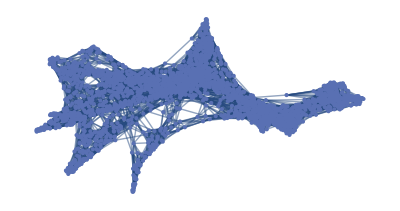

```mathematica
pancG=NearestNeighborGraph[P1[[All,1;;30]],10,VertexCoordinates->Automatic,GraphLayout->"SpringElectricalEmbedding"]//IndexGraph;
GraphPlot[pancG]
```

```mathematica
pancCoord=GraphEmbedding[pancG,"SpringElectricalEmbedding"];pancCoord//Short
```

{{12.7029,12.7866},{16.27,12.3222},«2528»,{14.7503,8.84453}}

### 3. Commute time embedding using custom function

```mathematica
commuteEmbed[graph_,n_]:=Module[{L,λ,U,s},L=KirchhoffMatrix[graph]//N;
{λ,U}=-Eigensystem[-L,n,Method->{"Arnoldi","MaxIterations"->10^6,"Criteria"->"RealPart"}];
{λ,U}=Reverse/@{λ,U}//Re;
s=(DiagonalMatrix[1/λ[[2;;]]]^(1/2)).U[[2;;]];{λ,U,s}]
```

```mathematica
{λ,ϕ,Θ}=commuteEmbed[pancG,15];
```

commute time kernel construction

```mathematica
Kct=Transpose[Θ].Θ;
Kct2=MatrixPower[Kct,1/2];
```

multiscale k-NN graph construction

```mathematica
tl=Transpose[{Θ[[1]],Θ[[2]]}];ListPlot[tl]
```

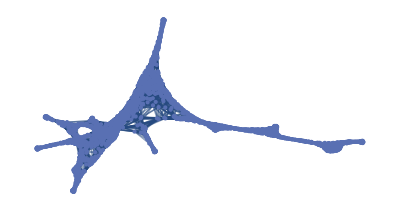

```mathematica
gr=NearestNeighborGraph[Transpose[Θ],30,VertexCoordinates->Automatic,GraphLayout->"SpringElectricalEmbedding"]//IndexGraph
```

```mathematica
map=GraphEmbedding[gr,"SpringElectricalEmbedding"];map//Short
```

{{16.2051,12.7094},{21.3565,22.9035},«2528»,{21.2242,14.9769}}

```mathematica
(*A=AdjacencyMatrix[gr]//Normal;
Export["adj_mat.csv",A,"CSV"]*)
```

explore gene expression using normalized gene expression

```mathematica
Position[pancGenes,_?(#=="Ghrl"&)][[1]][[1]]
```

19805

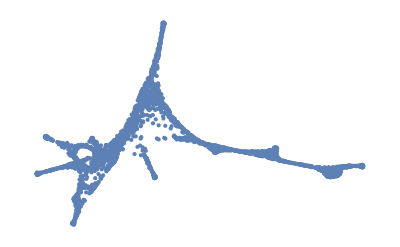

```mathematica
exp=pancNorm[[All,Position[pancGenes,_?(#=="Ins2"&)][[1]][[1]]]];
mapPlot=Nearest[map[[All,{1,2}]]->Rescale[exp]];
colfunArr=ColorData["Viridis"]@First@mapPlot[{#1,#2}]&;
ListPlot[map,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

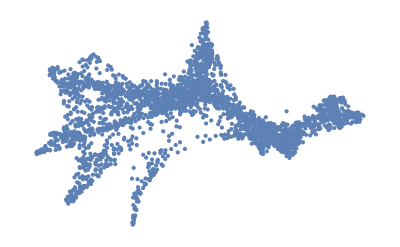

```mathematica
exp=pancNorm[[All,Position[pancGenes,_?(#=="Ins2"&)][[1]][[1]]]];
mapPlot=Nearest[pancCoord[[All,{1,2}]]->Rescale[exp]];
colfunArr=ColorData["Viridis"]@First@mapPlot[{#1,#2}]&;
ListPlot[pancCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

```mathematica
exp=pancNorm[[All,Position[pancGenes,_?(#=="Ins2"&)][[1]][[1]]]];
mapPlot=Nearest[tl[[All,{1,2}]]->Rescale[exp]];
colfunArr=ColorData["Viridis"]@First@mapPlot[{#1,#2}]&;
ListPlot[tl,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

### 4. Imputation of gene expression

```mathematica
imp=Kct2.pancNorm//Re;
```

```mathematica
scale=(Transpose@imp*Map[Quantile[#,0.99]&,Transpose[pancNorm]])/(Max[#,10^-8]&/@Transpose[imp])//Transpose;
```

```mathematica
posscale=Module[{x},(Transpose[scale]-Min/@Transpose[scale])*(((Max/@Transpose[scale])-0)/(x=MinMax[#,10^-8]&/@Transpose[scale];Differences/@x//Flatten))+0//Transpose];
Imputed=posscale;
```

```mathematica
Dimensions[Imputed]
```

{2531,27998}

plotting

```mathematica
exp=Imputed[[All,Position[pancGenes,_?(#=="Ppy"&)][[1]][[1]]]];
mapPlot=Nearest[pancCoord[[All,{1,2}]]->Rescale[exp]];
colfunArr=ColorData["Viridis"]@First@mapPlot[{#1,#2}]&;
ListPlot[pancCoord,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

-Graphics-

```mathematica
Export["Ins2_panc.pdf",%]
```

Ins2_panc.pdf

```mathematica
exp=Imputed[[All,Position[pancGenes,_?(#=="Ins2"&)][[1]][[1]]]];
mapPlot=Nearest[map[[All,{1,2}]]->Rescale[exp]];
colfunArr=ColorData["Viridis"]@First@mapPlot[{#1,#2}]&;
ListPlot[map,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

-Graphics-

```mathematica
Table[Labeled[GraphPlot[gr,VertexStyle->Thread[VertexList[gr]->ColorData["Viridis"]/@Rescale[Imputed[[All,Position[pancGenes,_?(#==ToString[i]&)][[1]][[1]]]]]],EdgeShapeFunction->None],Style[ToString[i],Italic]],
{i,{Ins1,Ins2,Gcg,Ghrl,Sst,Pyy,Sox9,Bicc1,Neurod2,Fev}}]
```

```mathematica
Export["isletFates2.pdf",%]
```

isletFates2.pdf

```mathematica
exp=Imputed[[All,Position[pancGenes,_?(#=="Procr"&)][[1]][[1]]]];
mapPlot=Nearest[map[[All,{1,2}]]->Rescale[exp]];
colfunArr=ColorData["Viridis"]@First@mapPlot[{#1,#2}]&;
ListPlot[map,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

-Graphics-

### 5. Pseudotime

```mathematica
CtPt=Table[Norm[Kct2[[10]]-Kct2[[j]],1],{j,2531}];
```

```mathematica
mapPlot=Nearest[map[[All,{1,2}]]->Rescale[CtPt]];
colfunArr=ColorData["Magma"]@First@mapPlot[{#1,#2}]&;
ListPlot[map,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

-Graphics-

```mathematica
GraphPlot[gr,VertexStyle->Thread[VertexList[gr]->ColorData["Viridis"]/@Rescale[CtPt]],EdgeShapeFunction->None]
```

### 6. Probability

```mathematica
tips=Import["data/selected_cells(panc2).txt","Data"];
```

```mathematica
tips[[1;;10]]
```

{{276},{2356},{1970},{814},{216},{2008},{1577},{1862},{1755},{666}}

add one to correct going form zero-indexing....

```mathematica
tips=(Flatten@tips)+1;tips//Short
```

{277,2357,1971,815,217,2009,1578,1863,1756,667,1408,768,1879,504,327,1987,«136»,274,2368,510,794,36,1958,243,1586,2451,2069,1022,1985,2438,71,2511,2513}

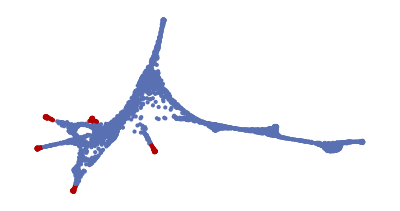

```mathematica
GraphPlot[gr,GraphHighlight->tips,EdgeShapeFunction->None]
```

```mathematica
subG=Subgraph[gr,tips];
clusts=FindGraphCommunities[subG];
cluspos=Select[clusts,(Length[#]>10)&];
```

```mathematica
testAbs=Table[RandomChoice[cluspos[[i]],10],{i,Length[cluspos]}];testAbs//Short
```

«1»

```mathematica
Length[testAbs]
```

5

```mathematica
probs=Table[Table[Kct2.(SparseArray[{i}->1,Length[Kct2]]),{i,testAbs[[j]]}],{j,Length[testAbs]}];
```

```mathematica
mapPlot=Nearest[map[[All,{1,2}]]->Rescale[Mean@probs[[5]]]];
colfunArr=ColorData["Magma"]@First@mapPlot[{#1,#2}]&;
ListPlot[map,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

-Graphics-

1 ==  epsilon ; 2 ==  gamma  ; 3 ==  beta  ; 4 ==  alpha ; 5 ==  delta

### 7. Trajectory correlations

trajectory 2 --  gamma fate

```mathematica
pp2=Rescale[Mean@probs[[2]]];
psta2=Table[Transpose[{pp2,(rsc=Rescale[pancNorm[[All,i]]])}],{i,Length@pancGenes}];
```

```mathematica
corr2=Correlation/@psta2;
```

```mathematica
corrs2=Table[corr2[[i,1]][[2]],{i,Length[corr2]}];
```

```mathematica
corrs2=corrs2/.Indeterminate->0;
ord2=Ordering[corrs2,-50]//Reverse;
ord2[[1;;5]]
```

{3714,11509,3713,27247,21425}

```mathematica
pancGenes[[ord2]]
```

{Pyy,Rbp4,Ppy,Tmem27,Abcc8,Ssr2,Meis2,Scg2,Pcsk2,Cpe,Dbpht2,Tmed3,1500009L16Rik,Fkbp2,Scgn,Gnas,1700086L19Rik,Gpx3,Fam183b,Scg5,Ghr,Scg3,Igfbp7,St6galnac5,Hadh,Pam,Dlk1,Pcsk1n,Fam92b,Slc16a10,Ripply3,Tspan8,Resp18,Tspan7,Trappc2l,Ffar1,Kctd8,Immp1l,Ddost,Mageh1,Rab37,Ndn,Ndufa1,Nenf,Peg10,Lgals3bp,Arxes2,Sphkap,Rnf130,Anxa4}

```mathematica
exp=Imputed[[All,Position[pancGenes,_?(#=="Pyy"&)][[1]][[1]]]];
mapPlot=Nearest[map[[All,{1,2}]]->Rescale[exp]];
colfunArr=ColorData["Viridis"]@First@mapPlot[{#1,#2}]&;
ListPlot[map,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

-Graphics-

```mathematica
Export["Pyy.pdf",%]
```

Pyy.pdf

trajectory 5 -- delta fate

```mathematica
pp5=Rescale[Mean@probs[[5]]];
psta5=Table[Transpose[{pp5,(rsc=Rescale[pancNorm[[All,i]]])}],{i,Length@pancGenes}];
corr5=Correlation/@psta5;
```

```mathematica
corrs5=Table[corr5[[i,1]][[2]],{i,Length[corr5]}];
```

```mathematica
corrs5=corrs5/.Indeterminate->0;
ord5=Ordering[corrs5,-50]//Reverse;
```

```mathematica
ord5[[1;;5]]
ReverseSort[corrs5][[1;;50]]
```

{8795,11509,3714,11899,14980}

{0.878326,0.522839,0.488093,0.419136,0.348886,0.333712,0.326096,0.302716,0.299746,0.294294,0.291595,0.289548,0.279111,0.278171,0.275171,0.272781,0.272079,0.267408,0.267121,0.263023,0.261686,0.254787,0.242417,0.232934,0.2327,0.230046,0.228153,0.22575,0.222952,0.221824,0.215621,0.213667,0.212978,0.212892,0.212411,0.211278,0.210721,0.208185,0.206354,0.203884,0.201877,0.200562,0.200562,0.200562,0.199831,0.198204,0.198204,0.198204,0.196859,0.192491}

```mathematica
pancGenes[[ord5]]
```

{Sst,Rbp4,Pyy,Hhex,Hadh,Ptprz1,Arg1,Kctd8,Fam159b,Igfbp5,Mest,1500009L16Rik,Ramp1,Frzb,Gpx3,Cfap61,Th,Scg2,Mef2c,Ssr2,Fam183b,Auts2,Dlk1,Meis2,Igfbp7,Meg3,Spock3,Isl1,Gap43,Ddost,Pcsk2,Cpne4,Pcdh15,Klhdc8b,Nrsn1,Sult1d1,1700086L19Rik,Cd24a,Tnfrsf26,Ghr,Stk32c,Ankrd34a,Aif1,Avpr1a,Oxtr,Gm44296,Ldb2,Olfm3,Cd200,Gm28959}

```mathematica
exp=Imputed[[All,Position[pancGenes,_?(#=="Cry2"&)][[1]][[1]]]];
mapPlot=Nearest[map[[All,{1,2}]]->Rescale[exp]];
colfunArr=ColorData["Viridis"]@First@mapPlot[{#1,#2}]&;
ListPlot[map,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

-Graphics-

### 8. Differential gene expression

```mathematica
data1=cluspos[[{1,5,3,4}]]//Flatten;data1//Short
data2=cluspos[[2]];data2//Short
```

{1863,1756,667,1408,327,1987,1841,2181,1789,230,2305,101,2199,«105»,1615,965,2068,514,1229,234,624,1929,1109,161,2317,274,71}

{292,1784,1833,1183,1170,1098,2329,2412,654,129,501,2474,2198,«11»,2236,2239,1889,1736,1310,2368,510,36,1958,1586,1022,2438,2513}

```mathematica
Xdata=Join[pancNorm[[data1]],pancNorm[[data2]]];
Dimensions@Xdata
Xnx=Standardize[Xdata,Mean,1&];
```

{168,27998}

```mathematica
Min[Dimensions[Xnx][[2]]-1,20]
```

20

```mathematica
{u,S,v}=SingularValueDecomposition[Xnx,10];
```

```mathematica
R=u.S;
```

```mathematica
meanvec=Mean[pancNorm[[data2]]]-Mean[pancNorm[[data1]]];
```

```mathematica
Dd=Transpose[R].R/(Length[data1]+Length[data2]);
Dd=DiagonalMatrix[Diagonal[Dd]];
```

```mathematica
σ=Mean[Diagonal[Dd]]
Dimensions[Dd]
```

29225.8

{10,10}

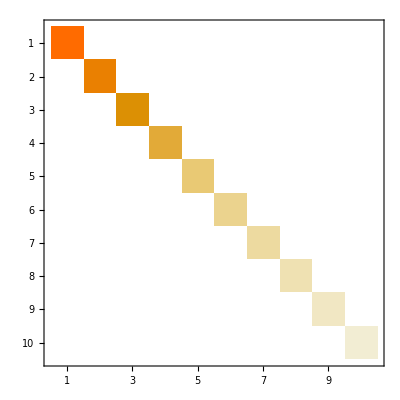

```mathematica
MatrixPlot[Dd]
```

```mathematica
(*ShrunkMats=Map[Inverse[#*Dd+σ(1-#)*IdentityMatrix[Length[Dd]]]&,1]; SKIP if gamma == 1   eq. 3 below *)
```

```mathematica
Dds=(0.5)Dd+0.5σ^2IdentityMatrix[Length[Dd]];
```

```mathematica
b=v.Inverse[Dds].Transpose[v].meanvec;b//Short
b=b/Norm[b];
```

{-3.44042×10^-22,4.33732×10^-22,6.43387×10^-22,«27992»,0.,0.,-2.65797×10^-10}

```mathematica
Total[b^2]
```

1.

```mathematica
Max[b]
```

0.887164

```mathematica
b//ReverseSort//Short
bord=b//Ordering//Reverse;bord//Short
```

{0.887164,0.0222929,0.0187949,«27993»,-0.210471,-0.318425}

{3714,3713,11509,14297,13992,11301,27247,9814,18319,25550,«27978»,10247,20304,21405,14159,22132,20804,8795,11990,12327,19805}

```mathematica
pancGenes[[bord[[1;;40]]]]
```

{Pyy,Ppy,Rbp4,Gnas,Chgb,Malat1,Tmem27,Hsp90ab1,Actb,Hspa8,1700086L19Rik,Chga,Cpe,Hsp90aa1,Ttr,Id2,Actg1,Rps4x,Rps14,Gast,Dbpht2,H1f0,Rpl14,Lrpprc,Rpl13a,Hmgn3,Rap1b,Ubb,H3f3b,Tspan7,Rps3a1,Hhex,Cartpt,Calm2,Rpl21,Anxa4,Eef1a1,Ywhaq,Fev,Ier2}

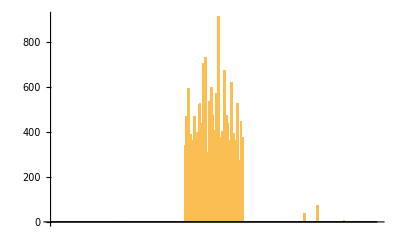

```mathematica
BarChart[Xdata[[;;,11990]]]
```

3- Beta cells: {Ins2,Ins1,Nnat,Iapp,Dlk1,Npy,Hspa5,Sdf2l1,Ctrb1,Hsp90b1,Ftl1,Pdia6} -- 10 PCs
	{Ins1,Iapp,Ins2,Nnat,Npy,Ftl1,Dlk1,Sec61b,Ppp1r1a,Calr,Sdf2l1,Pdia6,Hsp90b1,Hspa5,Rpl41,Pdia3,Gng12,Creld2,Tuba1a,Atp5g1} -- 10 PCs 0.5 gamma
	{Ins1,Iapp,Ins2,Nnat,Npy,Ftl1,Dlk1,Sec61b,Ppp1r1a,Calr,Sdf2l1,Pdia6} --keep
5- Delta Cells: {Sst,Pyy,Rbp4,Malat1,Cd24a,Hhex,Ppy,Rpl10,Fos,Rps14,Hadh} -- 10 PCs; 0.5 gamma
	{Sst,Pyy,Rbp4,Cd24a,Malat1,Hhex,Ppy,Rpl10,Dlk1,Rps14,Hadh,Fos} -- keep
2- gamma Cells:

#### significance:

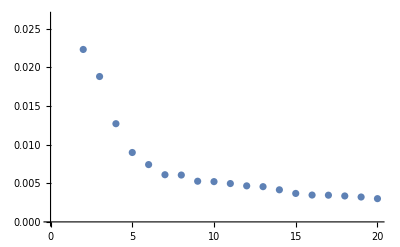

{0.887164,0.0222929,0.0187949,0.0126953,0.00897122,0.00740869,0.00609767,0.00605763,0.00525849,0.00520733,0.00495761,0.00465879,0.00455501,0.00414888,0.00368051,0.00347176,0.00345253,0.00335329,0.00321711,0.00300616}

```mathematica
ListPlot[ReverseSort[b][[1;;20]],PlotRange->Automatic]
ReverseSort[b][[1;;20]]
```

```mathematica
Intersection[pancGenes[[ord2]],pancGenes[[(bord[[1;;50]])]]]
```

{1700086L19Rik,Anxa4,Cpe,Dbpht2,Gnas,Ppy,Pyy,Rbp4,Tmem27,Tspan7}

### 9. Spliced v. unspliced graphs

#### a. importing and normalization

```mathematica
spliced=Module[{data,indices,indptr,rows,cols,dataSparse},data=Import[h5adFile,{"Datasets","/layers/spliced/data"}];indices=Import[h5adFile,{"Datasets","/layers/spliced/indices"}];
indptr=Import[h5adFile,{"Datasets","/layers/spliced/indptr"}];
rows=Length[indptr]-1;
cols=Max[indices]+1;
dataSparse=SparseArray[Automatic,{rows,cols},0,
{1,{indptr,Transpose[{indices+1}]},data}];dataSparse]
```

SparseArray[<5985054>, {2531, 27998}]

```mathematica
unspliced=Module[{data,indices,indptr,rows,cols,dataSparse},data=Import[h5adFile,{"Datasets","/layers/unspliced/data"}];indices=Import[h5adFile,{"Datasets","/layers/unspliced/indices"}];
indptr=Import[h5adFile,{"Datasets","/layers/unspliced/indptr"}];
rows=Length[indptr]-1;
cols=Max[indices]+1;
dataSparse=SparseArray[Automatic,{rows,cols},0,
{1,{indptr,Transpose[{indices+1}]},data}];dataSparse]
```

SparseArray[<2185408>, {2531, 27998}]

```mathematica
libsizeS=Total[spliced,{2}]//Median
libsizeU=Total[unspliced,{2}]//Median
```

5633.

1260.

```mathematica
SNorm=Table[Normalize[spliced[[i]]//N,Norm[#,1]&]*libsizeS,{i,Length[pancNorm]}]//N;
UNorm=Table[Normalize[unspliced[[i]]//N,Norm[#,1]&]*libsizeU,{i,Length[pancNorm]}]//N;
```

#### b. projecting into common principal component space

```mathematica
arr=ArrayFlatten[({{SNorm}, {UNorm}})];Dimensions[arr]
```

{5062,27998}

```mathematica
libsizeBoth=Total[arr,{2}]//Median
bothNorm=Table[Normalize[arr[[i]]//N,Norm[#,1]&]*libsizeBoth,{i,Length[arr]}]//N;
```

3446.5

```mathematica
Snx=bothNorm[[1;;Length[SNorm]]];
Unx=bothNorm[[(Length[SNorm]+1);;-1]];
```

```mathematica
Snx=Standardize[Snx,Mean,1&]; (* TO *)
Unx=Standardize[Unx,Mean,1&]; (* FROM *)
```

```mathematica
{υ,ζ,ν}=SingularValueDecomposition[Snx,30];
{υ1,ζ1,ν1}=SingularValueDecomposition[Unx,30];
```

```mathematica
Semb=Snx.ν;
Uemb=Unx.ν;
```

```mathematica
Sgraph=NearestNeighborGraph[Semb,10,VertexCoordinates->Automatic]//IndexGraph;
Ugraph=NearestNeighborGraph[Uemb,10,VertexCoordinates->Automatic]//IndexGraph;
```

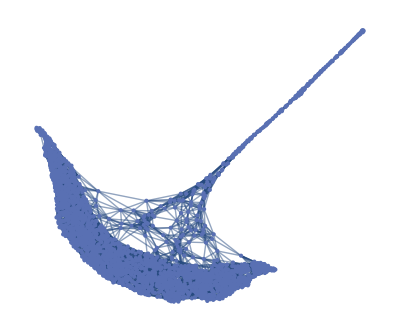
{-Graphics-,-Graphics-}

```mathematica
GraphPlot[#,GraphLayout->"SpringElectricalEmbedding"]&/@{Sgraph,Ugraph}
```

```mathematica
{embedS,embedU}=GraphEmbedding[#,"SpringElectricalEmbedding"]&/@{Sgraph,Ugraph};
```

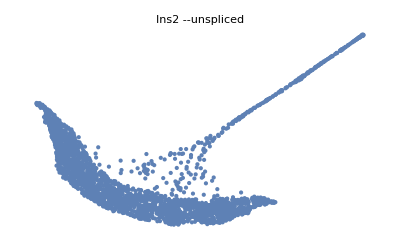

```mathematica
gene=Position[pancGenes,_?(#=="Ins2"&)][[1]];
arrPlot=Nearest[embedU[[All,{1,2}]]->Rescale[UNorm[[All,gene[[1]]]]]];
colfunArr=ColorData["Viridis"]@First@arrPlot[{#1,#2}]&;
lp=ListPlot[embedU[[All,{1,2}]],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotStyle->PointSize[Medium],Axes->None,PlotRange->All,PlotLabel->Style[pancGenes[[gene]][[1]],Italic] "--unspliced"]
```

#### c. graph kernels and imputation

```mathematica
{λs,Us,ss}=commuteEmbed[Sgraph,15];
{λu,Uu,su}=commuteEmbed[Ugraph,15];
```

```mathematica
(*{ss//MatrixPlot,su//MatrixPlot}*)
```

```mathematica
KpS=Transpose[ss].ss;
KpU=Transpose[su].su;
```

```mathematica
KpS2=MatrixPower[KpS,1/2];
KpU2=MatrixPower[KpU,1/2];
```

```mathematica
impS=KpS2.SNorm//Re;
scale=(Transpose@impS*Map[Quantile[#,0.99]&,Transpose[SNorm]])/(Max[#,10^-8]&/@Transpose[impS])//Transpose;
posscale=Module[{x},(Transpose[scale]-Min/@Transpose[scale])*(((Max/@Transpose[scale])-0)/(x=MinMax[#,10^-8]&/@Transpose[scale];Differences/@x//Flatten))+0//Transpose];
ImputedS=posscale;
```

```mathematica
impU=KpU2.UNorm//Re;
scale=(Transpose@impU*Map[Quantile[#,0.99]&,Transpose[UNorm]])/(Max[#,10^-8]&/@Transpose[impU])//Transpose;
posscale=Module[{x},(Transpose[scale]-Min/@Transpose[scale])*(((Max/@Transpose[scale])-0)/(x=MinMax[#,10^-8]&/@Transpose[scale];Differences/@x//Flatten))+0//Transpose];
ImputedU=posscale;
```

plotting .....

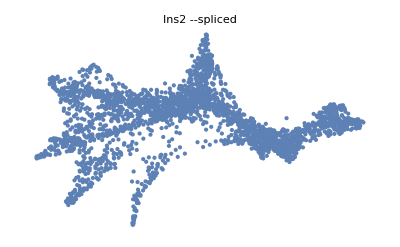

```mathematica
gene=Position[pancGenes,_?(#=="Ins2"&)][[1]];
arrPlot=Nearest[embedS[[All,{1,2}]]->Rescale[ImputedU[[All,gene[[1]]]]]];
colfunArr=ColorData["Viridis"]@First@arrPlot[{#1,#2}]&;
lp=ListPlot[embedS[[All,{1,2}]],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotStyle->PointSize[Medium],Axes->None,PlotRange->All,PlotLabel->Style[pancGenes[[gene]][[1]],Italic]"--spliced"]
```

```mathematica
Export["Gcg.pdf",%]
```

Gcg.pdf

#### d. pseudotime across graphs

```mathematica
vel=Table[Norm[KpS2[[j]]-KpU2[[j]],1],{j,Length[KpS2]}];
```

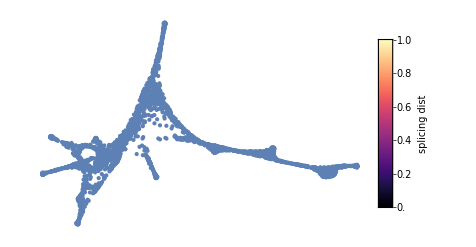

```mathematica
mapPlot=Nearest[map[[All,{1,2}]]->Rescale@(vel)];
colfunArr=ColorData["Magma"]@First@mapPlot[{#1,#2}]&;
ListPlot[map,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All,PlotLegends->BarLegend[{ColorData["Magma"],{0,1}},LegendLabel->"splicing dist"]]
```

```mathematica
Export["vol.pdf",%]
```

vol.pdf

-- Unspliced expression correlation:

```mathematica
psta=Table[Transpose[{Rescale[vel],Rescale[UNorm[[All,i]]]}],{i,Length[pancGenes]}];
corr=Correlation/@psta;
```

```mathematica
corrs=Table[corr[[i,1]][[2]],{i,Length[corr]}];
```

```mathematica
corrs=corrs/.Indeterminate->0;
ord=Ordering[corrs,-50]//Reverse;
ord[[1;;30]]
```

{22132,6461,12,14159,8250,17615,6288,10782,25736,16109,2807,26556,25456,4580,4752,11876,18145,15139,13545,8788,15259,5913,20557,9188,20804,20386,24731,23139,26881,2314}

```mathematica
pancGenes[[ord]]
```

{Ins2,Phactr1,Sntg1,Nnat,Ppp1r1a,Prkag2,Ero1lb,Mcc,Rora,Slc24a2,Grip1,Sytl4,7630403G23Rik,Car10,Mapt,Papss2,Atp2a2,Slc2a2,G6pc2,Dgkg,P2ry1,Gm15810,Gm43948,Dnajb11,Iapp,Gng12,Ntm,Prkcb,Arhgap36,Oprm1,P4hb,Robo2,Itpkb,Gm281,Pde7b,Arhgef3,Cntfr,Sntg2,Sec24d,Slc2a5,Thsd4,Sdk2,Bace2,RP23-2D23.2,Pcbp3,Tssc4,Trpm3,Igf1r,Hsp90b1,Galnt18}

```mathematica
Export["unspl.csv",pancGenes[[ord]],"CSV"]
```

unspl.csv

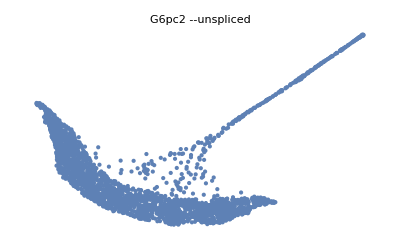

```mathematica
gene=Position[pancGenes,_?(#=="G6pc2"&)][[1]];
arrPlot=Nearest[embedU[[All,{1,2}]]->Rescale[ImputedU[[All,gene[[1]]]]]];
colfunArr=ColorData["Viridis"]@First@arrPlot[{#1,#2}]&;
lp=ListPlot[embedU[[All,{1,2}]],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotStyle->PointSize[Medium],Axes->None,PlotRange->All,PlotLabel->Style[pancGenes[[gene]][[1]],Italic]"--unspliced"]
```

```mathematica
Export["g6p.pdf",%]
```

g6p.pdf

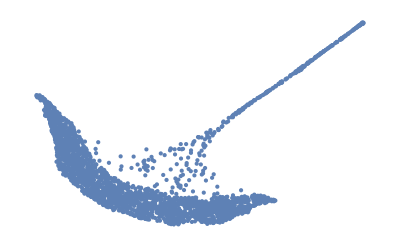

```mathematica
arrPlot=Nearest[embedU[[All,{1,2}]]->Rescale@vel];
colfunArr=ColorData["Magma"]@First@arrPlot[{#1,#2}]&;
lp=ListPlot[embedU[[All,{1,2}]],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotStyle->PointSize[Medium],Axes->None,PlotRange->All(*PlotLabel->Style[pancGenes[[gene]][[1]],Italic]"--unspliced"*)]
```

```mathematica
Export["unspl.pdf",%]
```

unspl.pdf

#### e. Circadian gene expression analyses

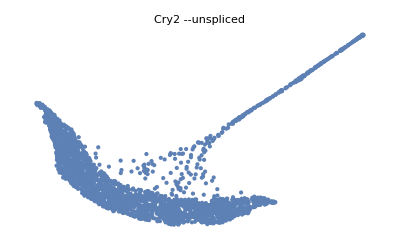

```mathematica
gene=Position[pancGenes,_?(#=="Cry2"&)][[1]];
arrPlot=Nearest[embedU[[All,{1,2}]]->Rescale[ImputedU[[All,gene[[1]]]]]];
colfunArr=ColorData["Viridis"]@First@arrPlot[{#1,#2}]&;
lp=ListPlot[embedU[[All,{1,2}]],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotStyle->PointSize[Medium],Axes->None,PlotRange->All,PlotLabel->Style[pancGenes[[gene]][[1]],Italic]"--unspliced"]
```

```mathematica
Export["Cry2.pdf",%]
```

Cry2.pdf

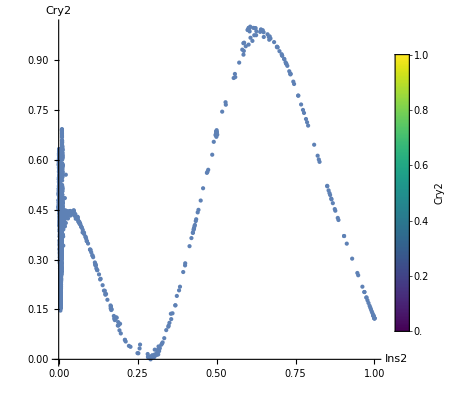

```mathematica
gene1=Position[pancGenes,_?(#=="Ins2"&)][[1]];
gene2=Position[pancGenes,_?(#=="Cry2"&)][[1]];
ta2=Transpose[{Rescale@ImputedU[[All,gene1[[1]]]],Rescale@ImputedU[[All,gene2[[1]]]]}];
ixPlot=Nearest[ta2[[All,{1,2}]]->Rescale[ImputedS[[All,gene2[[1]]]]]];
colfunArr=ColorData["Viridis"]@First@ixPlot[{#1,#2}]&;
ListPlot[ta2,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,PlotRange->All,AspectRatio->1,AxesLabel->{"Ins2","Cry2"},LabelStyle->style1,PlotLegends->BarLegend[{ColorData["Viridis"],{0,1}},LegendLabel->"Cry2"]]
```

```mathematica
Export["Ins2Cry2.pdf",%]
```

Ins2Cry2.pdf

```mathematica
Dxy=SmoothKernelDistribution[ta2,0.05,"Gaussian"];Dx=SmoothKernelDistribution[ta2[[All,1]],0.05,"Gaussian"];
Dy=SmoothKernelDistribution[ta2[[All,2]],0.05,"Gaussian"];
cond=PDF[Dxy,{xx,yy}]/Max[PDF[Dx,xx],10^-8];
```

```mathematica
DensityPlot[cond,{xx,0,1.},{yy,0,1.},PlotRange->All,Frame->False]
```

-Graphics-

```mathematica
DREMI=Quiet@NIntegrate[cond*Log[Max[PDF[Dxy,{xx,yy}],10^-8]/(Max[PDF[Dx,xx],10^-8]Max[PDF[Dy,yy],10^-8])],{xx,-Infinity,Infinity},{yy,-Infinity,Infinity}]
```

1.89481

```mathematica
jp=CDF[Dxy,ta2]; (* joint probability, i.e., nebulosa *)
```

```mathematica
mapPlot=Nearest[embedU[[All,{1,2}]]->Rescale[cp]];
colfunArr=ColorData["FakeParula"]@First@mapPlot[{#1,#2}]&;
ListPlot[embedU,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

-Graphics-

```mathematica
Export["cp2.pdf",%]
```

cp2.pdf

conditional Pr. Pr cry2 | on Ins2 epxression

```mathematica
cp=PDF[Dxy,ta2]/PDF[Dx,ta2[[All,1]]];
```

```mathematica
mapPlot=Nearest[embedS[[All,{1,2}]]->Rescale[cp]];
colfunArr=ColorData["FakeParula"]@First@mapPlot[{#1,#2}]&;
ListPlot[embedS,PlotStyle->PointSize[Medium],ColorFunction->colfunArr,ColorFunctionScaling->False,Axes->False,PlotRange->All]
```

-Graphics-

```mathematica
Export["jp.pdf",%]
```

jp.pdf

```mathematica
BarLegend[{ColorData["FakeParula"],{0,1}}]
```

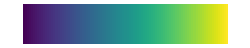

```mathematica
Show[ColorData["Viridis","Image"]]
```

### export to SPRING:

```mathematica
CreateDirectory["pancreas"]
```

/Users/houon/Library/Mobile Documents/com~apple~CloudDocs/Work/Manuscripts/CommuteTime/houston_2023/pancreas

#### # color_data_all_genes

```mathematica
II=Round[Length[pancGenes]/50]+1
```

561

```mathematica
Z=Insert[pancNorm,pancGenes,1]ᵀ;Z//Dimensions
```

{27998,2532}

```mathematica
pos=Position[Mean/@Z[[All,2;;]],_?(#>0.05&)]
```

```mathematica
Quantile[Mean/@Z[[All,2;;]],0.5]
```

0.00184142

```mathematica
ZZ=Extract[Z,pos];ZZ//Dimensions
```

{8256,2532}

```mathematica
parts=Partition[ZZ,II];parts//Dimensions
```

{14,561,2532}

```mathematica
(*CreateDirectory["pancreas/gene_colors"]*)
```

```mathematica
Module[{fname,customColors},Do[
fname="pancreas/gene_colors/color_data_all_genes-"<>ToString[j-1]<>".csv";
customColors=parts[[j]];
Export[fname,customColors,"CSV","TextDelimiters"->""],{j,Length[parts]}]]
```

#### # color stats

```mathematica
colorStats=Module[{mean,std,min,max,centile,colorStats},colorStats=List[];Do[mean=Mean[pancNorm[[All,i]]];
std=StandardDeviation[pancNorm[[All,i]]];
min=Min[pancNorm[[All,i]]];max=Max[pancNorm[[All,i]]];centile=Quantile[pancNorm[[All,i]],0.996];
AppendTo[colorStats,{mean,std,min,max,centile}];,{i,Length[pancGenes]}];colorStats];
colorStats//Short
```

{{0.00151514,0.0381817,0.,1.04508,0.},«27996»,{0.355192,«19»,0.,«18»,3.31028}}

```mathematica
testThread=Table[Thread[pancGenes[[i]]->colorStats[[i]],List,1],{i,Length[pancGenes]}];
testThread//Short
```

{Xkr4→{0.00151514,0.0381817,0.,1.04508,0.},Gm37381→{«1»},«27995»,Erdr1→{0.355192,«4»}}

```mathematica
Export["pancreas/color_stats.json",testThread, "JSON","Compact"->False]
```

pancreas/color_stats.json

#### # write graph

{  “nodes”: [ {   “name”: cell0, “number”: 0 },     // List of nodes
                   {   “name”: cell1, “number”: 1 },
                   ....
                   {   “name”: cellN, “number”: N } ],
        “links”: [ { “source”: 10, “target”: 23 },      // List of edges
                   { “source”: 29, “target”: 50 },
                   ....
                   { “source”: 40, “target”: 125 }  ] }

```mathematica
names=VertexList[gr];
numbers=VertexList[gr]; 

Export["pancreas/graph_data.json",{"nodes"->MapThread[{"name"->#1-1,"number"->#2-1}&,{names,numbers}],"links"->({"source"->#1-1,"target"->#2-1,"distance"->0}&)@@@EdgeList[gr]},"JSON"]
```

pancreas/graph_data.json

#### # coordinates

```mathematica
newmap=Transpose[Insert[Transpose[map*100],Range[0,Length[map]-1],1]];
```

```mathematica
Export["pancreas/coordinates.txt",Flatten/@newmap,"CSV"]
```

pancreas/coordinates.txt

```mathematica
(*Export["cell_filter.txt",Range[Length[geneList]]-1]*)
```

cell_filter.txt

#### # save custom colors (opt., OK)

custom_colors[‘Uniform’] = np.zeros(E.shape[0])
    write_color_tracks(custom_colors, project_directory+‘color_data_gene_sets.csv’)
    
    use {} to ensure commas

```mathematica
customColors1=ConstantArray[0,Dimensions[pancNorm][[1]]]//Prepend[#,"Uniform"]&;
customColors2=Rescale@CtPt//Prepend[#,"pseudotime"]&;
customColorSet=Join[{customColors1},{customColors2}];
```

```mathematica
customColors2//Short
```

{pseudotime,0.862037,0.803622,«2526»,0.766496,0.961263,0.814939}

```mathematica
Export["pancreas/color_data_gene_sets.csv",{customColors2},"CSV","TextDelimiters"->""]
```

pancreas/color_data_gene_sets.csv

In[15]:= Import[“file.h5”, {“DataEncoding”, “/input_image”}]

```mathematica
test=Import["/Users/houon/Documents/counts_norm_sparse_genes.hdf5",{"DataEncoding","/counts/"}]
```

```mathematica
test2=Import["/Users/houon/Documents/counts_norm_sparse_cells.hdf5","/counts"]
```

Export[“m1.h5”, “/m1” -> {
   “Data” -> Range[5], 
   “DataFormat” -> “UnsignedInteger8”
   }]

```mathematica
counts=Table[marrowNorm[[i,All]],{i,Dimensions[marrowNorm][[1]]}];
Export["counts_norm_sparse_genes.hdf5","/counts"->marrowNorm,"/gene_ix"->marrowGenes]
```

counts_norm_sparse_genes.hdf5

### ChDir-Example

```mathematica
example=Import["/Users/houon/Documents/MATLAB/chdir_matlab/example.txt","Data"];
example[[1;;5,1;;5]]
```

{{0 marks control,1 marks experiment,0,0,0,0},{PSME1,11.0434,11.2627,10.8087,11.4478},{CISD1,10.2767,9.8619,9.8398,9.735},{VDAC1,12.5042,12.4814,12.5263,12.3535},{SORBS3,6.4963,6.4695,5.823,6.3342}}

```mathematica
example[[1,2;;]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1}

```mathematica
data=example[[2;;,2;;]]ᵀ
```

```mathematica
Dimensions@data
```

{26,978}

```mathematica
Dnx=Standardize[data,Mean,1&];
```

```mathematica
{u,S,v}=SingularValueDecomposition[Dnx,20];
```

```mathematica
R=u.S;
```

```mathematica
crtl=data[[1;;20]];
expm=data[[21;;]];
meanvec=Mean[expm]-Mean[crtl];
Dimensions@meanvec
```

{978}

```mathematica
Dd=Rᵀ.R/26;
```

```mathematica
Dd=DiagonalMatrix[Diagonal[Dd]];Dd//MatrixForm
```

(44.4151 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 25.8593 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 16.2149 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 14.4117 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 13.0014 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 12.44 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 10.6287 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.45316 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.78071 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.5351 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.86366 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.52168 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.21493 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.62268 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.33472 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.11072 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.01653 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.56959 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.38878 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.92281)

```mathematica
sig= Mean@Diagonal[Dd]
```

11.3653

```mathematica
ShrunkMats=Map[Inverse[#.Dd+sig(1-#).IdentityMatrix[Dimensions[R]][[2]]]&,1]
```

1

```mathematica
Dd.IdentityMatrix[20]
```

{{44.4151,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,25.8593,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,16.2149,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,14.4117,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,13.0014,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,12.44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,10.6287,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,9.45316,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,8.78071,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,8.5351,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.86366,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.52168,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.21493,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.62268,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.33472,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.11072,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.01653,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.56959,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.38878,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.92281}}

```mathematica
b=Map[v.#.Transpose[v].meanvec&,Dd]
```

Dot::dotsh: Tensors {-2.17915,1.1619,0.518922,-1.19801,-0.295457,-1.2622,-0.231079,0.159848,-0.509956,-1.55808,«968»} and {{-0.0490632,0.0261601,0.0116835,-0.0269732,-0.00665217,-0.0284184,-0.00520271,0.00359897,-0.0114816,-0.03508,«968»},{0.005676,-0.0125783,0.0162302,0.0140357,-0.0211175,-0.00957476,-0.0066216,0.0223141,-0.0137943,0.0137123,«968»},«8»,«10»} have incompatible shapes.

Dot::dotsh: Tensors {-2.17915,1.1619,0.518922,-1.19801,-0.295457,-1.2622,-0.231079,0.159848,-0.509956,-1.55808,«968»} and {-7.35568,-0.330735,-3.76195,-5.48626,-2.9747,-0.628467,-0.837904,-0.874382,0.138005,1.27914,«10»} have incompatible shapes.

Dot::dotsh: Tensors {0.146777,-0.325267,0.419703,0.362954,-0.546085,-0.247597,-0.17123,0.577027,-0.356712,0.354592,«968»} and {{-0.0490632,0.0261601,0.0116835,-0.0269732,-0.00665217,-0.0284184,-0.00520271,0.00359897,-0.0114816,-0.03508,«968»},{0.005676,-0.0125783,0.0162302,0.0140357,-0.0211175,-0.00957476,-0.0066216,0.0223141,-0.0137943,0.0137123,«968»},«8»,«10»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
b=v.Dd.Transpose[v].meanvec;
```

```mathematica
b//Short
```

{15.0875,-7.27772,-13.2133,«972»,0.451992,3.78333,6.40317}

```mathematica
b/Norm[b]//ReverseSort//Short
```

{0.241911,0.19336,0.131675,«972»,-0.137054,-0.144582,-0.158317}

```mathematica
Dimensions[R]
R//MatrixForm
```

{26,20}

(11.3555 | -2.62541 | 4.02048 | -7.83802 | 6.47572 | -0.0331902 | -0.754698 | 4.60002 | -0.169345 | -1.55165 | 1.37632 | 1.04326 | 1.29017 | -4.34734 | -1.31927 | -3.89923 | -2.15255 | 2.83977 | 0.625024 | -3.11244
9.29862 | 3.45816 | 0.888376 | 3.51116 | 1.50556 | -0.0735496 | -7.31276 | -3.70107 | -1.94932 | 6.03317 | 2.79701 | -4.11257 | -3.1554 | 1.83675 | -1.12446 | 1.32079 | 0.345209 | 0.100983 | -0.874344 | -3.87463
7.67971 | -9.62843 | 4.15825 | 1.80585 | -4.47766 | -0.409638 | 4.75821 | -0.506873 | 0.793697 | 2.20394 | 0.0332503 | -1.7194 | -1.29802 | -3.64463 | -2.82145 | 0.169326 | 4.74105 | -3.09051 | 2.31537 | 0.0322722
4.68983 | -3.95417 | 2.52136 | -2.63208 | -0.20002 | 1.6179 | -6.8337 | 5.66727 | -1.07188 | -5.07084 | 2.78657 | -0.465094 | -2.45609 | 2.02789 | 0.0536411 | 4.94023 | 0.654996 | -2.23005 | 0.791303 | 4.02609
11.1014 | -1.79249 | 1.13729 | 0.531819 | -6.20242 | -5.61591 | 2.48148 | -4.80242 | -1.79678 | -3.58893 | -0.139959 | 4.95447 | -1.70048 | 2.4249 | 0.487909 | 2.60314 | -1.87214 | 4.78623 | 0.103521 | -1.50695
3.83795 | 3.35121 | 2.20414 | 0.442749 | -2.59028 | -5.63167 | -2.54022 | 2.0073 | 1.19474 | 2.61742 | 0.800031 | 3.52356 | 3.74657 | -0.541014 | 7.616 | -2.51719 | 4.02716 | -2.61188 | -0.811818 | -0.0757572
5.58668 | 10.1183 | 1.86542 | -6.69882 | 7.78325 | 1.15046 | 7.424 | -2.16946 | 0.0654281 | 1.68696 | -1.41876 | 0.214427 | -2.00711 | 4.21092 | 0.957872 | 1.9793 | 1.84449 | -2.0752 | 0.464843 | 1.2941
4.14848 | 5.18832 | 1.7079 | 0.75569 | -1.42083 | 5.30224 | -3.48798 | -4.10758 | 5.49672 | -3.53004 | -4.99057 | -3.8906 | 0.375418 | -2.77957 | 4.36712 | -0.0917336 | -1.36972 | 1.85918 | 0.463691 | 1.45952
-1.01047 | -0.990664 | -0.397855 | 2.18796 | 2.743 | -3.66801 | 0.256815 | -1.1646 | 1.35734 | -0.455185 | 2.57053 | -6.02134 | 5.67009 | 1.40127 | -1.00712 | 0.198225 | -0.605074 | 0.779841 | 1.27087 | -0.12862
-0.912489 | 6.06149 | -2.27729 | 5.99282 | 3.11395 | -4.70527 | 1.15399 | -2.01187 | 5.00928 | -4.24572 | 3.67238 | 1.17977 | -3.43672 | -2.96774 | -2.89091 | -2.26026 | 0.485507 | -0.423831 | 1.76645 | 2.54629
0.544563 | -0.562231 | -3.10627 | 2.43164 | 3.40512 | -0.40905 | -3.20664 | -1.84229 | -0.332818 | -1.73123 | -2.01198 | 3.62701 | 0.793332 | 0.955643 | -3.56479 | -2.32698 | 0.872549 | -3.29167 | -4.25348 | 0.813972
-0.541881 | -6.32207 | -1.7295 | 2.58223 | 3.32672 | 2.60193 | 0.125185 | -0.257588 | 0.234345 | -0.331244 | 0.7362 | 2.93302 | -0.153038 | 1.27142 | 1.44956 | -0.254149 | -1.87569 | -0.0712946 | -5.23532 | 0.167675
-6.72019 | -0.6689 | -0.52665 | 2.24931 | 1.83051 | 1.26524 | -0.584056 | -1.04248 | -0.26546 | -3.28367 | -0.918168 | 2.47087 | 3.68922 | 1.09333 | -0.354809 | 2.11487 | 0.662464 | -3.1313 | 3.32441 | -5.00692
-0.317275 | 7.30751 | 0.79507 | 2.6189 | -3.97943 | 4.19121 | 5.48985 | 2.03856 | -5.24086 | -3.22875 | 4.91298 | -3.26689 | 2.05953 | -2.06497 | 0.474176 | 0.247632 | 1.3371 | 0.891166 | -4.96522 | -0.018688
-5.83834 | -2.37264 | 7.10671 | 2.38197 | -1.30951 | -5.20265 | 1.73833 | 4.00812 | -0.828728 | -2.23511 | -5.94934 | -4.51871 | -2.55974 | 4.48934 | -0.263376 | -3.648 | -1.93674 | -0.919783 | -1.32245 | -0.911924
-5.24085 | -1.98225 | 0.129825 | 3.7604 | 5.17087 | -1.9452 | -0.489135 | -0.916841 | -8.18669 | 2.77954 | -4.14513 | 0.592501 | -2.17206 | -5.52848 | 2.10261 | 1.37951 | -0.372894 | 1.37716 | 1.22483 | 2.81774
5.42721 | -12.0483 | -2.29122 | 2.53117 | 0.707396 | 6.78518 | 3.37394 | -2.03412 | 1.40399 | 2.58049 | 1.74541 | -0.0847325 | 0.849944 | 2.7486 | 2.34757 | -2.69752 | -2.40538 | -0.276736 | 1.31244 | 2.2038
8.29061 | 5.29562 | -7.92228 | 4.68092 | -1.85668 | -0.26547 | 1.59899 | 8.6622 | 2.95452 | 4.4441 | -3.65763 | 0.916496 | 1.45245 | 0.345658 | -2.10792 | 2.58588 | -1.66321 | 1.68407 | 0.48163 | 0.452933
-12.2453 | -1.56742 | 4.02055 | 1.76956 | 1.01567 | 3.28712 | 1.32377 | 2.54074 | 2.77728 | 0.26048 | 1.20637 | 1.98799 | -1.84183 | 0.243907 | 1.8167 | 3.45193 | 1.57117 | 2.23654 | 1.63114 | -1.98042
-5.18447 | 5.26084 | 5.05852 | 2.25601 | -1.31153 | 4.65895 | -0.648125 | -0.931394 | -2.08241 | 0.742545 | -0.725418 | 2.7308 | 3.31284 | -0.627402 | -2.71806 | 0.0509152 | -2.95906 | -0.916931 | 1.91216 | -0.808057
-2.80005 | -3.80445 | -0.488922 | -7.53104 | -2.35316 | -2.87783 | -0.143498 | -3.3757 | 2.06517 | 1.22538 | -3.06171 | -1.17441 | 4.00277 | -2.56623 | -2.81002 | 4.35727 | -0.390319 | -1.05042 | -3.41462 | 1.28926
-10.5646 | -0.840559 | -1.23535 | -2.91624 | 0.468148 | -5.50747 | -0.426249 | -0.413519 | -0.643273 | 2.56195 | 4.50701 | -0.706768 | 2.18244 | 1.86753 | 0.799589 | -0.149283 | -2.42711 | 2.14511 | 1.8157 | 3.05009
-11.7645 | -0.451684 | 1.2789 | -3.04096 | -1.71477 | 0.503456 | -0.0960588 | 0.508253 | 5.12135 | 3.68755 | 1.73181 | 0.784656 | -4.75655 | -1.74242 | -0.305049 | -0.193496 | -0.195079 | 1.05041 | -3.31823 | -1.84679
-2.06753 | 0.584535 | -10.7399 | -4.82056 | -3.65111 | -0.644512 | 1.14325 | 0.109829 | -2.25309 | -1.8036 | 0.597938 | -1.98035 | -3.54728 | -1.80286 | 2.69766 | -0.727235 | -3.6553 | -4.58122 | 1.76955 | -2.78932
-4.56256 | -2.77751 | -8.15974 | -2.8059 | 0.551166 | 1.89629 | -1.64212 | -0.148428 | -1.64793 | -2.14831 | -2.38685 | -1.26052 | 0.11754 | 2.06714 | -0.847569 | -2.17161 | 7.3179 | 4.81512 | 0.742129 | -0.829647
-2.19002 | 5.7632 | 1.98219 | -4.20653 | -7.02968 | 3.72945 | -2.70257 | -0.716043 | -2.00528 | 2.38078 | -0.0682824 | 2.24256 | -0.458006 | 1.62836 | -3.0356 | -4.46233 | 0.0206942 | 0.105238 | 2.18041 | 2.73643)

```mathematica
v[[1;;5,1;;5]]
```

{{-0.0490632,0.005676,-0.030077,0.0187756,0.0315579},{0.0261601,-0.0125783,-0.0377182,0.00381001,0.0110471},{0.0116835,0.0162302,0.0939555,0.0408568,0.02841},{-0.0269732,0.0140357,-0.010186,0.00316236,0.0167728},{-0.00665217,-0.0211175,-0.0180301,0.0208862,-0.000954008}}

```mathematica
Dimensions[v]
```

{978,20}

```mathematica
b=v.Inverse[Dd].Transpose[v].meanvec;
b//Short
```

{-0.00139156,-0.00660149,«974»,0.0003043,0.00724289}

```mathematica
b=b/Norm[b];
```

{0.436542,0.310047,0.242719,«972»,-0.0860411,-0.0872997,-0.0886217}

```mathematica
b//Ordering//Reverse//Short
```

{555,580,444,635,564,224,928,972,559,583,743,284,855,244,865,253,13,«944»,136,474,301,741,221,69,760,502,511,271,736,420,628,755,814,779,931}

```mathematica
Total[b^2]
```

1.

```mathematica
genes=example[[2;;,1]];
```

```mathematica
genes[[555]]
```

EGR1

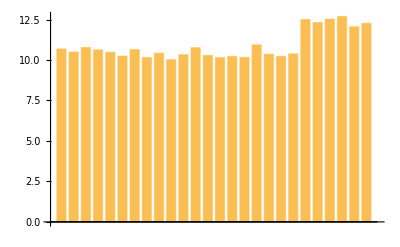

```mathematica
BarChart[data[[;;,635]]]
```

```mathematica
Range[Length[pancGenes]]
```

$Aborted

### extras

```mathematica
Dimensions[ν1]
```

{27998,30}

```mathematica
sp=ν1[[All,1]]//Ordering[#,-20]&
```

{3515,15827,24549,24336,12894,61,6801,10872,9628,25264,2967,25550,875,16699,3378,18456,18211,5718,21682,11301}

```mathematica
ν1[[All,1]][[3515]]
```

0.00447153

```mathematica
pancGenes[[sp]]
```

{Ins2,Nnat,Phactr1,Rora,Pcsk2,Sntg1,Gng12,Grip1,Ero1lb,Gnas,Ppp1r1a,Trpm3,Pde10a,Papss2,Tenm3,Mcc,Atp2a2,Robo2,Klhl32,Mapt}

```mathematica
Import[h5adFile]
```

{/X/data,/X/indices,/X/indptr,/layers/spliced/data,/layers/spliced/indices,/layers/spliced/indptr,/layers/unspliced/data,/layers/unspliced/indices,/layers/unspliced/indptr,/obs/G2M_score,/obs/S_score,/obs/__categories/clusters,/obs/__categories/clusters_coarse,/obs/__categories/clusters_fine,/obs/__categories/day,/obs/__categories/louvain_Alpha,/obs/__categories/louvain_Beta,/obs/__categories/phase,/obs/__categories/proliferation,/obs/clusters,/obs/clusters_coarse,/obs/clusters_fine,/obs/day,/obs/index,/obs/louvain_Alpha,/obs/louvain_Beta,/obs/palantir_pseudotime,/obs/phase,/obs/proliferation,/obsm/X_pca,/obsm/X_umap,/obsp/connectivities/data,/obsp/connectivities/indices,/obsp/connectivities/indptr,/obsp/distances/data,/obsp/distances/indices,/obsp/distances/indptr,/uns/clusters_colors,/uns/clusters_fine_colors,/uns/day_colors,/uns/louvain_Alpha_colors,/uns/louvain_Beta_colors,/uns/neighbors/connectivities_key,/uns/neighbors/distances_key,/uns/neighbors/params/method,/uns/neighbors/params/metric,/uns/neighbors/params/n_neighbors,/uns/neighbors/params/n_pcs,/uns/pca/variance,/uns/pca/variance_ratio,/var/__categories/highly_variable_genes,/var/highly_variable_genes,/var/index}